# initialize

```mathematica
If[$KernelCount==0,LaunchKernels[]];
```

```mathematica
func[img_Image]:=Module[{positions},
positions=ImageMeasurements[Binarize@img,"PerimeterPositions"];
Map[Arrow@Through[{First,Last}[#]]&@*(Take[#,Round[Length[#]/2]]&),positions]
];
```

```mathematica
createrotateArrowFunc[nearestFn_,scale_]:=With[{nF=nearestFn,s=scale},
rotateArrows[{pt1_,pt2_}]:=Module[{mean,rotTrans,transTransf,p1,p2},
mean=Mean[{pt1,pt2}];
transTransf=First@nF[mean];
p1=pt1+(transTransf-mean);
p2=pt2+(transTransf-mean);
mean=Mean[{p1,p2}];
rotTrans=RotationTransform[-90Degree,mean];
{p1,p2}=rotTrans[{p1,p2}];
{s Normalize[p1-mean]+p1,s Normalize[p2-mean]+p2}
]
]
```

```mathematica
fitRadius[cell_,rad_]:=Module[{cellcentre},
cellcentre=RegionCentroid[cell];
Show[HighlightMesh[cell,{Style[1,Dashed,Blue]}],Graphics[{Thick,Circle[cellcentre,rad]}],ImageSize-> Tiny]
];
```

```mathematica
dividePoly[reg_,reg2_,mean_,rotTrans_,pt_,pt2_,rad_,data_]:=Module[{intersects,pts,ptsOrdered,poly,nearestFn,
infiniteline,q1,q2,q3,selectpt,m,rotTrans2,intersects2,pi1,pi2,dim=1600},
pts=DeleteDuplicates[MeshPrimitives[reg,0]/.Point-> Sequence];
ptsOrdered=pts[[Last@FindShortestTour[pts]]];
poly=Polygon@ptsOrdered;
intersects=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],poly,#}]]&[InfiniteLine[{mean,rotTrans@pt}]];
nearestFn=Nearest[ptsOrdered];
infiniteline=InfiniteLine[{mean,pt}];
q1=First@TakeSmallestBy[Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],
MeshPrimitives[reg,2],#}]]&[infiniteline],EuclideanDistance[pt2,#]&,1];
{q2,q3}=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],MeshPrimitives[reg2,2],#}]]&[infiniteline];
selectpt=First@Extract[{q2,q3},Position[#,Min@#]&@(EuclideanDistance[q1,#]&/@{q2,q3})];
m=Mean[{q1,selectpt}];
rotTrans2=RotationTransform[-90Degree,m];
Print[InfiniteLine[{rotTrans2@pt,m}]];
intersects2=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],poly,#}]]&[InfiniteLine[{rotTrans2@pt,m}]];
Print[
Show[reg,Graphics[{{Dashed,Blue,InfiniteLine[{mean,rotTrans@pt}]},{Red,Dashed,Line[{mean,pt}]},
{Red,PointSize[0.04],Point@intersects2},{Dashed,Darker@Green,InfiniteLine[{rotTrans2@pt,m}]},
{Black,Circle[Abs[#-{0,dim}],rad]&/@data}}],ImageSize-> Small]
];
{pi1,pi2}=Flatten@Position[ptsOrdered,Alternatives@@Flatten[nearestFn@intersects2,1]];
Print@Graphics[{Red,Line@ptsOrdered[[pi1;;pi2]],Blue,Line@(ptsOrdered[[pi2;;]]~Join~ptsOrdered[[;;pi1]]),
PointSize[0.025],Black,Point@intersects2,{Black,Circle[Abs[#-{0,dim}],rad]&/@data}},ImageSize->Small];
{Polygon@ptsOrdered[[pi1;;pi2]],Polygon@(ptsOrdered[[pi2;;]]~Join~ptsOrdered[[;;pi1]])}
]
```

```mathematica
plotMesh[reg_,reg2_,reg3_,reg4_,rad_]:=Module[{regeff},
regeff=RegionDifference[Region@reg,reg2];
Show[HighlightMesh[DiscretizeRegion@Region[reg3],Style[{{1},{2}},LightBlue]],
HighlightMesh[DiscretizeRegion@Region[regeff],Style[{{1},{2}},LightGreen]],
HighlightMesh[DiscretizeRegion@Region[reg2],Style[{{1},{2}},LightRed]],
HighlightMesh[reg4,Style[{1},Black]],ImageSize-> Tiny]
];
```

```mathematica
regionMemberFn[reg_,reg2_,reg3_,reg4_,rad_,data_]:=Module[{plt,regeff,Mreg1,Mreg3,Mreg2,dim=1600},
regeff=RegionDifference[Region@reg,reg2];
plt=plotMesh[reg,reg2,reg3,reg4,rad];
Print@Show[plt,Graphics[{Black,Circle[Abs[#-{0,dim}],rad]&/@data}],ImageSize-> Small];
(*Print[{Area[#],Region[#,ImageSize->Tiny]}&/@{reg,reg2,Region@reg3}];*)
{RegionMember/@{regeff,reg2,reg3},Area/@{regeff,reg2,reg3}}
];
```

```mathematica
createRegion[mask_,ecad_]:=Block[{},
{Subscript[ℛ, 1],Subscript[ℛ, 2]}=ImageMesh/@{mask,ecad};
Print[Show[Subscript[ℛ, 1],HighlightMesh[Subscript[ℛ, 2],Style[2,LightPurple]],ImageSize-> Tiny]];
Subscript[ℛ, 3]=RegionBoundary[Subscript[ℛ, 1]];
Subscript[ℛ, 4]=ImageMesh[Thinning@MorphologicalPerimeter@mask];
]
```

```mathematica
convertPoly[reg_]:=Module[{pts,ptsOrdered},
pts=DeleteDuplicates[MeshPrimitives[reg,0]/.Point-> Sequence];
ptsOrdered=pts[[Last@FindShortestTour[pts]]];
Polygon@ptsOrdered
]
```

```mathematica
ClearAll[drawArrows];
drawArrows[data_,arrows_,rad_,plt_:None,imgsize_:Small,sizeArrow_:10]:=Block[{nearestFn,dim=1600,arrowsRotated,h},
nearestFn=Nearest[Abs[#-{0,dim}]&/@data];
createrotateArrowFunc[nearestFn,sizeArrow];
arrowsRotated=MapAt[rotateArrows,arrows,{All,1}];
h=Graphics[{Red,Polygon[{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]}];
If[plt=!=None,
Show[plt,Graphics[{{Darker@Blue,Circle[Abs[#-{0,dim}],rad]&/@data},
{Thickness[0.004],Arrowheads[{{-.015,0,{h,1}},{.015,1,{h,1}}},Appearance->"Projected"],arrowsRotated}}],
ImageSize->imgsize],
Show[Subscript[ℛ, 1],HighlightMesh[Subscript[ℛ, 2],Style[2,LightPurple]],
Graphics[{{Darker@Blue,Circle[Abs[#-{0,dim}],rad]&/@data},
{Thickness[0.004],Arrowheads[{{-.015,0,{h,1}},{.015,1,{h,1}}},Appearance->"Projected"],arrowsRotated}}],
ImageSize->imgsize]
]
];
```

# division maps

```mathematica
dir="C:\\Users\\aliha\\Desktop\\research related\\raw data\\@division events\\";
```

## set 1

```mathematica
mask=Import[dir<>"Set 1\\imageset1\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset1\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

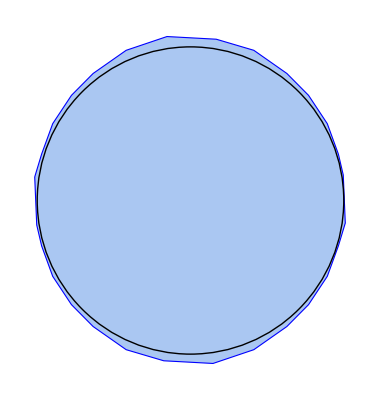

```mathematica
cell=ImageMesh@Import[dir<>"Set 1\\imageset1\\cell.tif"];
rad=40;fitRadius[cell,rad]
```

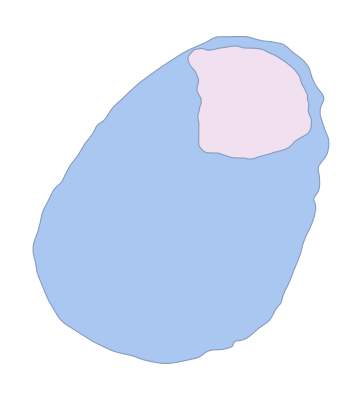

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 1\\imageset1\\imageset1.xlsx","Data"]][[All,3;;4]];
```

```mathematica
arrows=Flatten@ParallelMap[func,Import[dir<>"Set 1\\imageset1\\division vector of set 1\\*.tif"]];
```

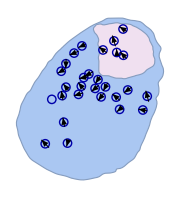

```mathematica
drawArrows[data,arrows,rad]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→1299.58,y→1518.27,u→237.553,v→209.224}

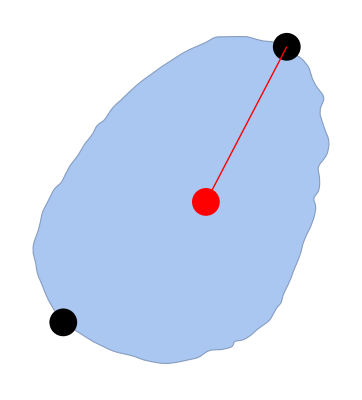

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@centroid,Line[{centroid,p1}]}],
ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,centroid]
```

TransformationFunction[(0. | -1. | 1696.59
1. | 0. | -133.963
0. | 0. | 1.)]

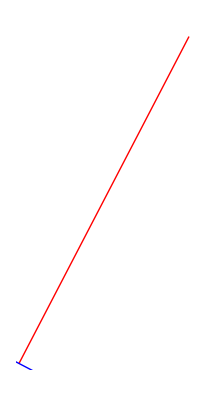

```mathematica
Graphics[{Red,Line[{centroid,p1}],Blue,InfiniteLine[{centroid,rot@p1}]},ImageSize->Tiny]
```

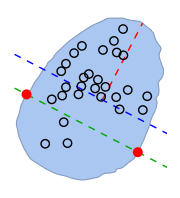

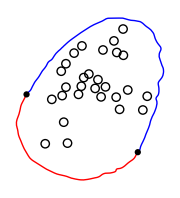

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],centroid,rot,p1,p2,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

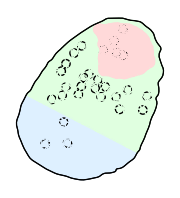

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{806139.,244008.,513550.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
plt=plotMesh[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad];
```

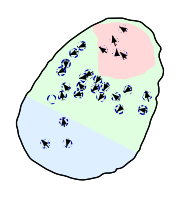

```mathematica
drawArrows[data,arrows,rad,plt]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{5,0.0000204911}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{20,0.0000248096}

```mathematica
{cRear,dRear}={#,#1/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{3,5.8417×10^-6}

```mathematica
dMid/dRear
```

4.24699

## set 2

```mathematica
mask=Import[dir<>"Set 1\\imageset2\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset2\\Ecad Mask.tif"];
```

```mathematica
temp=-Graphics-;
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

```mathematica
cell=ImageMesh[Import[dir<>"Set 1\\imageset2\\cell.tif"]];
```

```mathematica
cellcentre=RegionCentroid@cell;
```

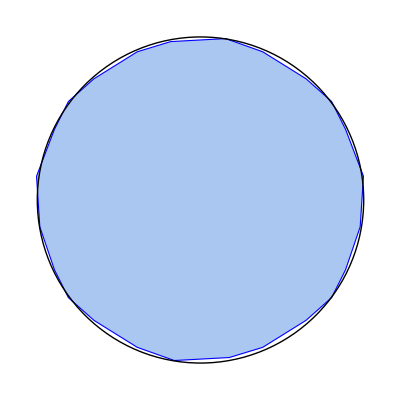

```mathematica
rad=35;
Show[HighlightMesh[cell,{Style[1,Dashed,Blue]}],Graphics[{Thick,Circle[cellcentre,rad]}],ImageSize->Tiny]
```

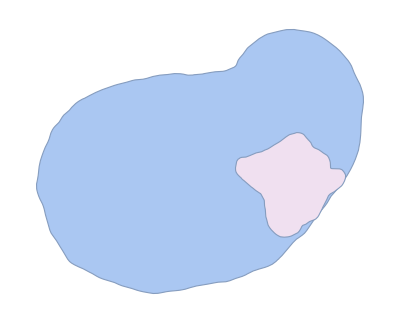

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=Cases[Import[dir<>"Set 1\\imageset2\\CellCounter_ch1 ph3 ch2 ecad ch3 ecad 96 hrs image 2-1.xml","XML"],XMLElement["Marker",{},{XMLElement["MarkerX",{},{x_}],XMLElement["MarkerY",{},{y_}],XMLElement["MarkerZ",{},{z_}]}]:> {ToExpression[x],ToExpression[y]},{0,Infinity},Heads->True];
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
arrows=Flatten@ParallelMap[func,Import[dir<>"Set 1\\imageset2\\division vector of set 2\\*.tif"]];
nearestFn=Nearest[Abs[#-{0,1600}]&/@data]
```

NearestFunction[…]

```mathematica
nearestFn~createrotateArrowFunc~30
```

```mathematica
arrowsRotated=MapAt[rotateArrows,arrows,{All,1}];
```

```mathematica
h=Graphics[{Red,Polygon[{{-1,1/2},{0,0},{-1,-1/2},{-1,1/2}}]}];
```

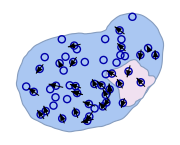

```mathematica
Show[Subscript[ℛ, 1],HighlightMesh[Subscript[ℛ, 2],Style[2,LightPurple]],
Graphics[{{Darker@Blue,Circle[Abs[#-{0,1600}],rad]&/@data},
{Thickness[0.004],Arrowheads[{{-.015,0,{h,1}},{.015,1,{h,1}}},Appearance->"Projected"],arrowsRotated}}],
ImageSize->Small]
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→1470.24,y→1144.56,u→38.5,v→682.}

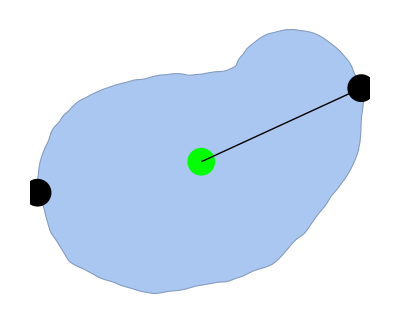

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],{Green,Point@centroid},Line[{centroid,p1}]}],
ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,centroid]
```

TransformationFunction[(0. | -1. | 1581.6
1. | 0. | 56.451
0. | 0. | 1.)]

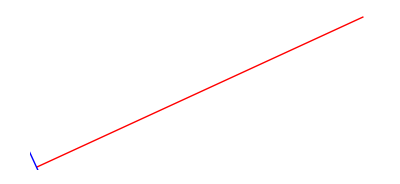

```mathematica
Graphics[{Red,Line[{centroid,p1}],Blue,InfiniteLine[{centroid,rot@p1}]},ImageSize->Tiny]
```

```mathematica
pts=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//DeleteDuplicates;
```

```mathematica
ptsOrdered=pts[[Last@FindShortestTour[pts]]];
```

```mathematica
poly=Polygon@ptsOrdered
```

Polygon[…]

```mathematica
nF=Nearest[ptsOrdered];
```

```mathematica
intersects=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],poly,#}]]&[InfiniteLine[{centroid,rot@p1}]]
```

{{586.13,1202.59},{986.35,332.571}}

```mathematica
(*q1=MeshCoordinates@RegionIntersection[RegionBoundary[Subscript[ℛ, 1]],Line[{p1,p1+10000((mean-p1)/Norm[mean-p1])}]]//First*)
```

```mathematica
(*{q2,q3}=MeshCoordinates@RegionIntersection[RegionBoundary[ImageMesh@temp],Line[{p1,p1+10000((mean-p1)/Norm[mean-p1])}]]*)
```

```mathematica
infiniteline=InfiniteLine[{centroid,p1}];
```

```mathematica
q1=First@TakeSmallestBy[Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],MeshPrimitives[Subscript[ℛ, 1],2],#}]]&[infiniteline],EuclideanDistance[p2,#]&,1];
```

```mathematica
{q2,q3}=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],MeshPrimitives[ImageMesh@temp,2],#}]]&[infiniteline];
```

```mathematica
selectpt=First@Extract[{q2,q3},Position[#,Min@#]&@(EuclideanDistance[q1,#]&/@{q2,q3})];
```

```mathematica
m=Mean[{q1,selectpt}];
```

```mathematica
rot2=RotationTransform[-90Degree,m]
```

TransformationFunction[(0. | 1. | -211.535
-1. | 0. | 1162.28
0. | 0. | 1.)]

```mathematica
intersects2=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],poly,#}]]&[InfiniteLine[{rot2@p1,m}]];
```

```mathematica
infline=InfiniteLine[{rot2@p1,m}];
```

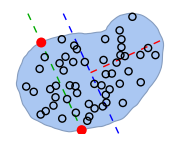

```mathematica
Show[Subscript[ℛ, 1],Graphics[{{Dashed,Blue,InfiniteLine[{centroid,rot@p1}]},{Red,Dashed,Line[{centroid,p1}]},
{Red,PointSize[0.04],Point@intersects2},{Dashed,Darker@Green,infline},
{Black,Circle[Abs[#-{0,1600}],rad]&/@data}}],ImageSize-> Small]
```

```mathematica
{pi1,pi2}=Flatten@Position[ptsOrdered,Alternatives@@Flatten[nF@intersects2,1]];
```

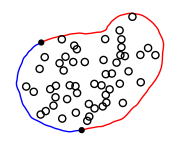

```mathematica
Graphics[{Red,Line@ptsOrdered[[pi1;;pi2]],Blue,Line@(ptsOrdered[[pi2;;]]~Join~ptsOrdered[[;;pi1]]),
PointSize[0.025],Black,Point@intersects2,{Black,Circle[Abs[#-{0,1600}],rad]&/@data}},ImageSize->Small]
```

```mathematica
{Subscript[ℛ, half1],Subscript[ℛ, half2]}={Polygon@ptsOrdered[[pi1;;pi2]],Polygon@(ptsOrdered[[pi2;;]]~Join~ptsOrdered[[;;pi1]])}
```

{Polygon[…],Polygon[…]}

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Region[Subscript[ℛ, half1]],Subscript[ℛ, 2]];
```

```mathematica
plt=Show[HighlightMesh[DiscretizeRegion@Region[Subscript[ℛ, half2]],Style[{{1},{2}},LightBlue]],
HighlightMesh[DiscretizeRegion@Region[Subscript[ℛ, half1eff]],Style[{{1},{2}},LightGreen]],
HighlightMesh[DiscretizeRegion@Region[Subscript[ℛ, 2]],Style[{{1},{2}},LightRed]],
HighlightMesh[Subscript[ℛ, 4],Style[{1},Black]],ImageSize-> Tiny];
```

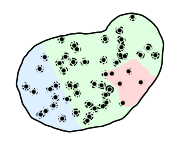

```mathematica
Show[plt,Graphics@{Black,Circle[Abs[#-{0,1600}],rad]&/@data,Point@dataModified},ImageSize-> Small]
```

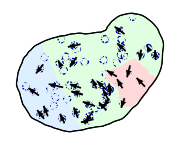

```mathematica
Show[plt,
Graphics[{{Darker@Blue,Circle[Abs[#-{0,1600}],rad]&/@data},
{Thickness[0.007],Arrowheads[{{-.015,0,{h,1}},{.015,1,{h,1}}},Appearance->"Projected"],arrowsRotated}}],
ImageSize->Small]
```

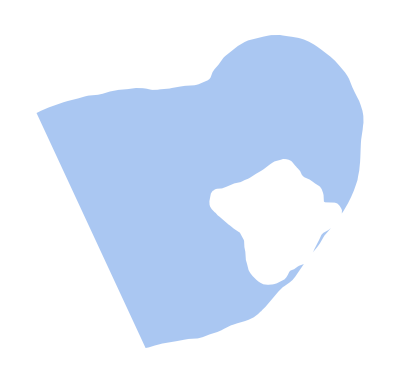
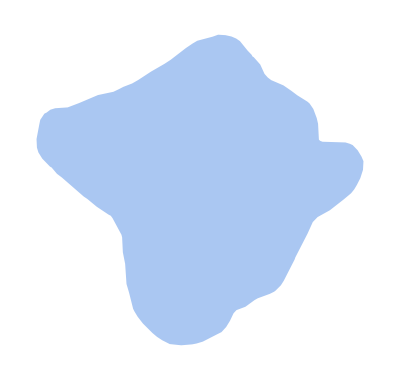
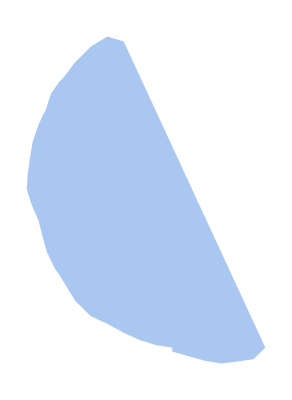
{{750359.,-Graphics-},{127751.,-Graphics-},{303905.,-Graphics-}}

```mathematica
{Area[#],Region[#,ImageSize->Tiny]}&/@{Subscript[ℛ, half1eff],Subscript[ℛ, 2],Region@Subscript[ℛ, half2]}
```

```mathematica
{Subscript[Mℛ, half1eff],Subscript[Mℛ, half2],Subscript[Mℛ, 2]}=RegionMember/@{Subscript[ℛ, half1eff],Subscript[ℛ, half2],Subscript[ℛ, 2]}
```

{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]}

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],Area[Subscript[ℛ, 2]]]
```

{5,0.0000391386}

```mathematica
{cMid,dMid}={#1,(#1)/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],Area[Subscript[ℛ, half1eff]]]
```

{35,0.0000466443}

```mathematica
{cRear,dRear}={#1,(#1)/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],Area[Subscript[ℛ, half2]]]
```

{12,0.0000394861}

```mathematica
dMid/dRear
```

1.18129

## set 3

```mathematica
mask=Import[dir<>"Set 1\\imageset3\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset3\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

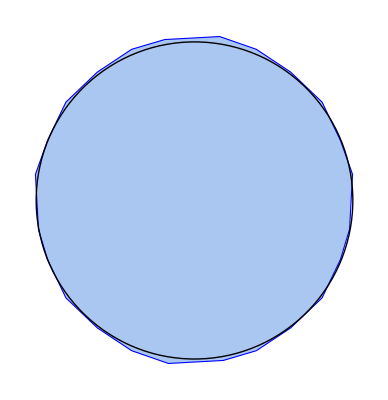

```mathematica
cell=ImageMesh@Import[dir<>"Set 1\\imageset3\\cell.tif"];
rad=34;fitRadius[cell,rad]
```

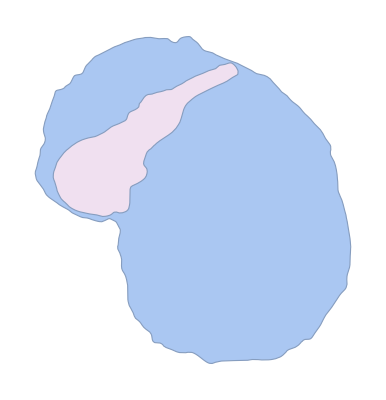

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 1\\imageset3\\imageset3.xlsx","Data"]][[All,3;;4]];
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→288.224,y→1490.45,u→1275.,v→207.5}

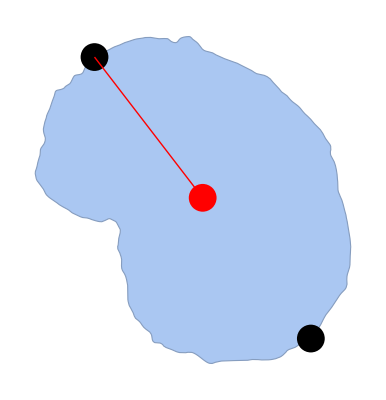

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p1}]}],
ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1630.59
1. | 0. | 67.3618
0. | 0. | 1.)]

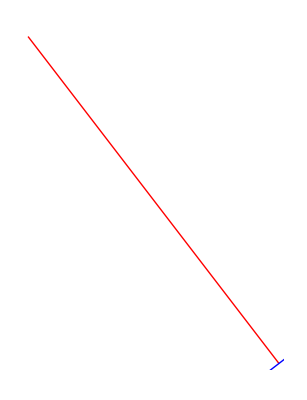

```mathematica
Graphics[{Red,Line[{mean,p1}],Blue,InfiniteLine[{mean,rot@p1}]},ImageSize->Tiny]
```

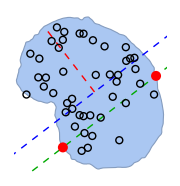

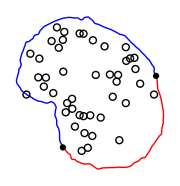

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p1,p2,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

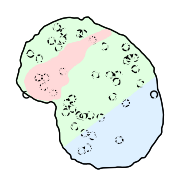

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{801484.,196827.,482638.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{6,0.0000304837}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{30,0.0000374306}

```mathematica
{cRear,dRear}={#,#1/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{7,0.0000145036}

```mathematica
dMid/dRear
```

2.58077

## set 4

```mathematica
mask=Import[dir<>"Set 1\\imageset4\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset4\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

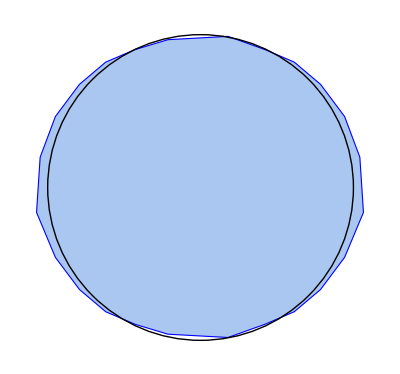

```mathematica
cell=ImageMesh@Import[dir<>"Set 1\\imageset4\\cell.tif"];
rad=30;fitRadius[cell,rad]
```

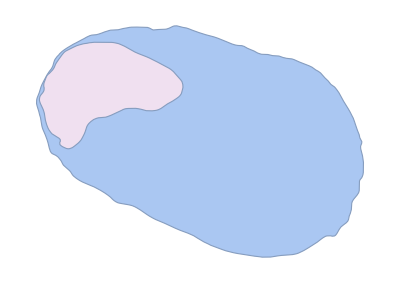

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 1\\imageset4\\imageset4.xls","Data"]][[All,3;;4]];
```

```mathematica
arrows=Flatten@ParallelMap[func,Import[dir<>"Set 1\\imageset4\\division vector of set 4\\*.tif"]];
```

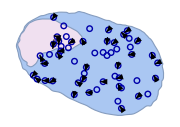

```mathematica
drawArrows[data,arrows,rad]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→97.803,y→1095.46,u→1523.47,v→307.176}

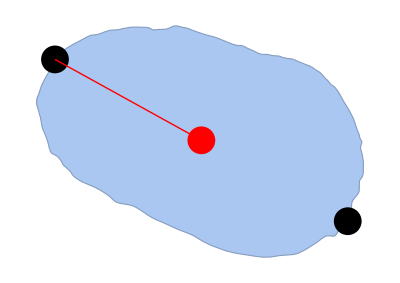

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p1}]}],
ImageSize->Tiny]
```

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
```

```mathematica
distmat=DistanceMatrix@meshCoords[[;;Round[Length[meshCoords]/2]]];
```

```mathematica
pos=FirstPosition[distmat,Max@distmat];
```

```mathematica
{p1,p2}=meshCoords[[pos]];
```

```mathematica
mean=Mean[{p1,p2}];
```

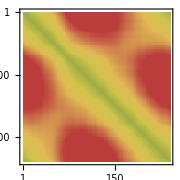

```mathematica
MatrixPlot[distmat,ImageSize->Small,ColorFunction->"DarkRainbow"]
```

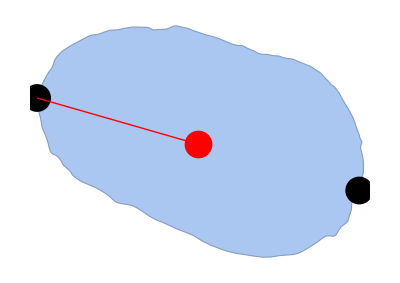

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Black,Point@{p1,p2},Red,Line[{mean,p2}],Red,Point@mean}],ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1477.18
1. | 0. | -113.02
0. | 0. | 1.)]

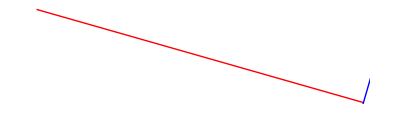

```mathematica
Graphics[{Red,Line[{mean,p2}],Blue,InfiniteLine[{mean,rot@p2}]},ImageSize->Tiny]
```

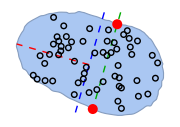

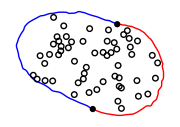

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p2,p1,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

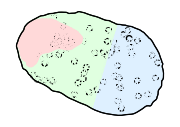

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
plt=plotMesh[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad];
```

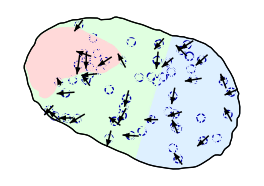

```mathematica
drawArrows[data,arrows,rad,plt,Medium,30]
```

```mathematica
{cTip,dTip}={#1,(#1)/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{8,0.0000374586}

```mathematica
{cMid,dMid}={#,(#)/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{25,0.0000450647}

```mathematica
{cRear,dRear}={#,(#1)/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{23,0.0000432092}

```mathematica
dMid/dRear
```

1.04294

## set 5

```mathematica
mask=Import[dir<>"Set 1\\imageset5\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset5\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

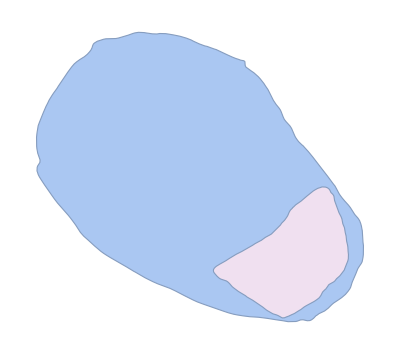

```mathematica
createRegion[mask,ecad]
```

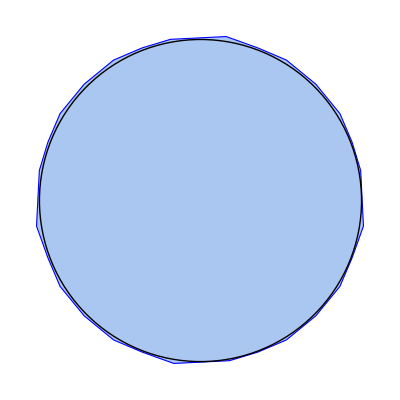

```mathematica
cell=ImageMesh@Import[dir<>"Set 1\\imageset5\\cell.tif"];
rad=37;fitRadius[cell,rad]
```

```mathematica
data=First[Import[dir<>"Set 1\\imageset5\\imageset5.xlsx","Data"]][[All,3;;4]];
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
arrows=Flatten@ParallelMap[func,Import[dir<>"Set 1\\imageset5\\division vector of set 5\\*.tif"]];
```

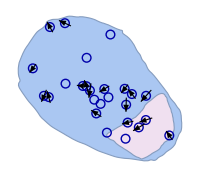

```mathematica
drawArrows[data,arrows,rad,None,200,20]
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→1433.45,y→311.21,u→253.54,v→1268.8}

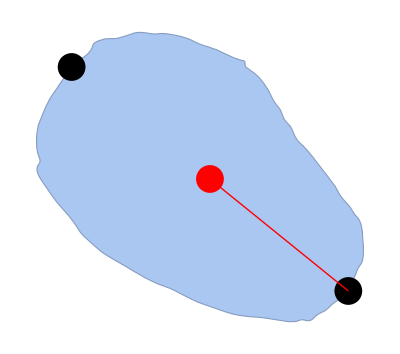

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p1}]}],
ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1633.5
1. | 0. | -53.4899
0. | 0. | 1.)]

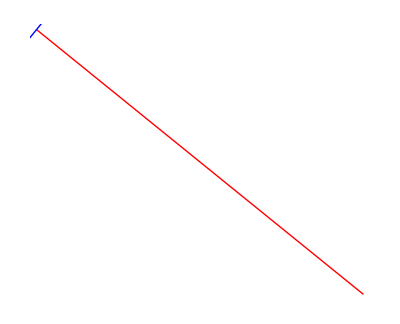

```mathematica
Graphics[{Red,Line[{mean,p1}],Blue,InfiniteLine[{mean,rot@p1}]},ImageSize->Tiny]
```

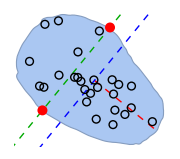

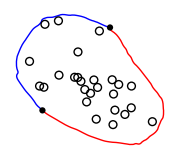

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half1],Subscript[ℛ, half2]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p1,p2,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

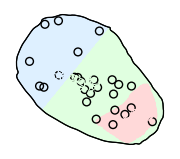

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{548221.,174421.,446606.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
plt=plotMesh[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad];
```

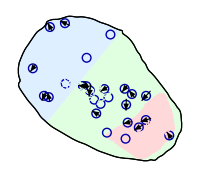

```mathematica
drawArrows[data,arrows,rad,plt,200]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{5,0.0000286663}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{13,0.0000237131}

```mathematica
{cRear,dRear}={#,#1/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{8,0.0000179129}

```mathematica
dMid/dRear
```

1.3238

## set 6

```mathematica
(* Aggregate does not seem good; excluded because of shape *)
```

```mathematica
mask=Import[dir<>"Set 1\\imageset6\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset6\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

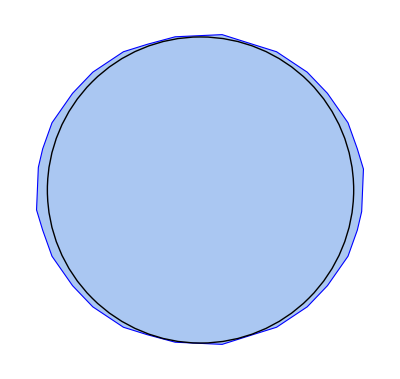

```mathematica
cell=ImageMesh@Import[dir<>"Set 1\\imageset6\\cell.tif"];
rad=45;fitRadius[cell,rad]
```

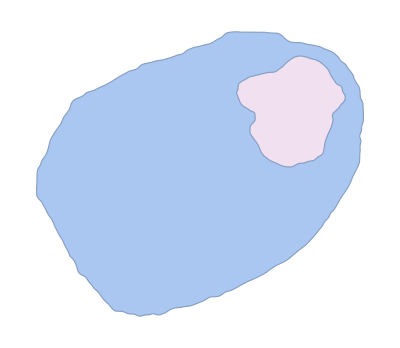

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 1\\imageset6\\imageset6.xlsx","Data"]][[All,3;;4]];
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→371.224,y→116.553,u→1487.78,v→1305.45}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
```

```mathematica
meshcent=Mean[meshCoords];
```

```mathematica
distmat=DistanceMatrix@meshCoords[[;;Round[Length[meshCoords]/2]]];
```

```mathematica
pos=FirstPosition[distmat,Max@distmat];
```

```mathematica
{p1,p2}=meshCoords[[pos]];
```

```mathematica
mean=Mean[{p1,p2}];
```

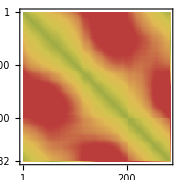

```mathematica
MatrixPlot[distmat,ImageSize->Small,ColorFunction->"DarkRainbow"]
```

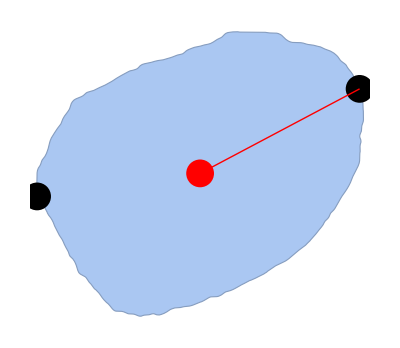

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@meshcent,Line[{meshcent,p2}]}],
ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,meshcent]
```

TransformationFunction[(0. | -1. | 1565.5
1. | 0. | -13.585
0. | 0. | 1.)]

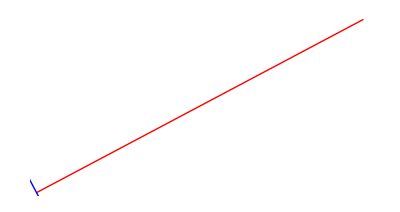

```mathematica
Graphics[{Red,Line[{meshcent,p2}],Blue,InfiniteLine[{meshcent,rot@p2}]},ImageSize->Tiny]
```

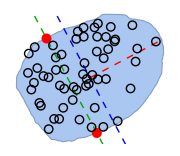

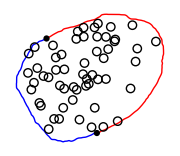

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half1],Subscript[ℛ, half2]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],meshcent,rot,p2,p1,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

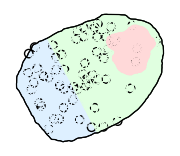

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{839764.,185874.,527452.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{4,0.00002152}

```mathematica
{cMid,dMid}={#+1,(#+1)/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{32,0.000038106}

```mathematica
{cRear,dRear}={#-1,(#1-1)/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{20,0.0000379182}

```mathematica
dMid/dRear
```

1.00495

## set 7

```mathematica
mask=Import[dir<>"Set 1\\imageset7\\Whole Mask.tif"];
ecad=Import[dir<>"Set 1\\imageset7\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

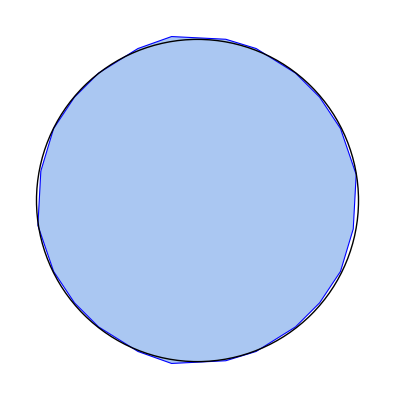

```mathematica
cell=ImageMesh@Import[dir<>"Set 1\\imageset7\\cell.tif"];
rad=38;fitRadius[cell,rad]
```

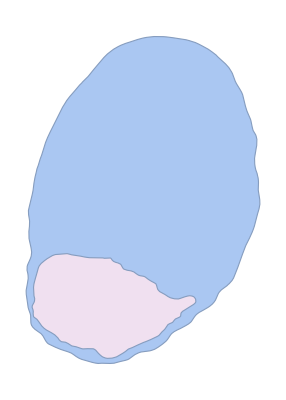

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 1\\imageset7\\imageset7.xlsx","Data"]][[All,3;;4]];
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→350.,y→183.5,u→970.,v→1494.5}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
```

```mathematica
distmat=DistanceMatrix@meshCoords[[;;Round[Length[meshCoords]/2]]];
```

```mathematica
pos=FirstPosition[distmat,Max@distmat];
```

```mathematica
{p1,p2}=meshCoords[[pos]];
```

```mathematica
mean=Mean[{p1,p2}];
```

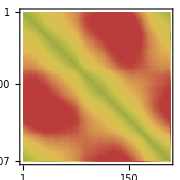

```mathematica
MatrixPlot[distmat,ImageSize->Small,ColorFunction->"DarkRainbow"]
```

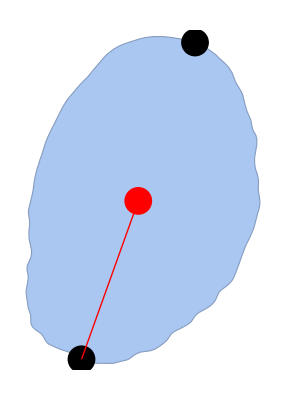

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p1}]}],ImageSize->Tiny]
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1525.08
1. | 0. | 107.059
0. | 0. | 1.)]

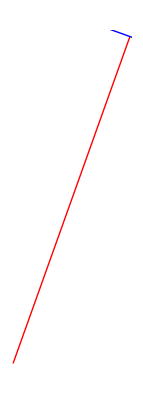

```mathematica
Graphics[{Red,Line[{mean,p1}],Blue,InfiniteLine[{mean,rot@p1}]},ImageSize->Tiny]
```

InfiniteLine[{{-110.512,1346.22},{784.106,1025.62}}]

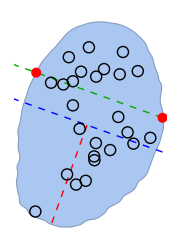

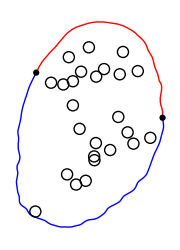

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p1,p2,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

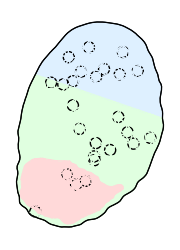

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{542093.,202823.,348688.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{3,0.0000147912}

```mathematica
{cMid,dMid}={#,(#1)/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{13,0.0000239811}

```mathematica
{cRear,dRear}={#,(#1)/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{9,0.000025811}

```mathematica
dMid/dRear
```

0.929104

## set 8

```mathematica
mask=Import[dir<>"Set 2\\imageset1\\Whole Mask.tif"];
ecad=Import[dir<>"Set 2\\imageset1\\Ecad Mask3.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

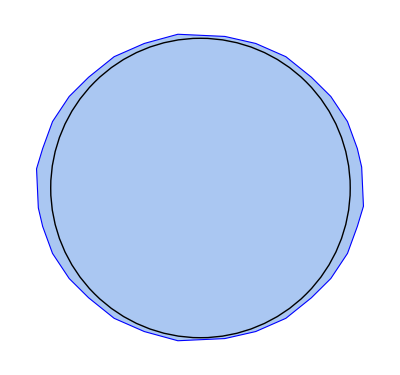

```mathematica
cell=ImageMesh@Import[dir<>"Set 2\\imageset1\\cell.tif"];
rad=44;fitRadius[cell,rad]
```

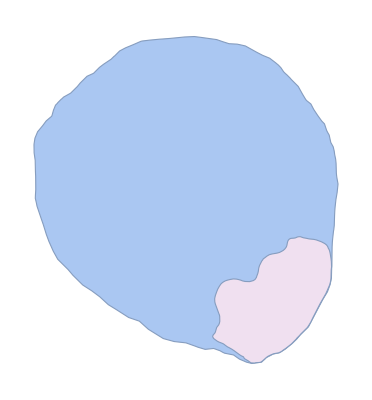

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 2\\imageset1\\imageset1.xlsx","Data"]][[All,3;;4]];
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→533.34,y→1468.37,u→1223.5,v→105.037}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
```

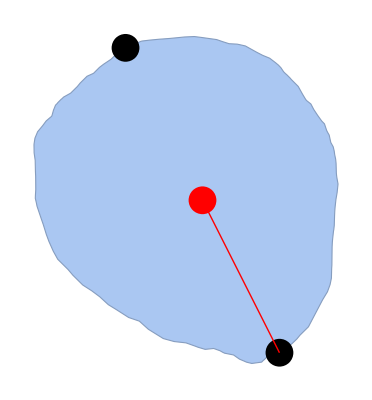

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p2}]}],
ImageSize->Tiny]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1665.12
1. | 0. | -91.7189
0. | 0. | 1.)]

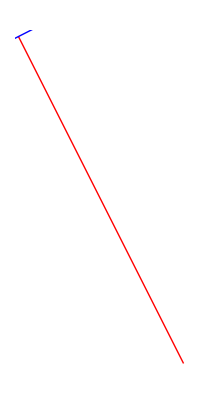

```mathematica
Graphics[{Red,Line[{mean,p2}],Blue,InfiniteLine[{mean,rot@p2}]},ImageSize->Tiny]
```

InfiniteLine[{{-44.6078,520.744},{797.3,946.945}}]

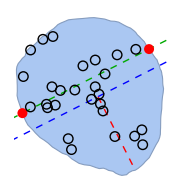

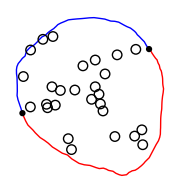

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half1],Subscript[ℛ, half2]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p2,p1,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

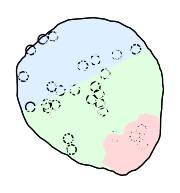

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{740237.,188692.,588966.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{4,0.0000211986}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{12,0.000016211}

```mathematica
{cRear,dRear}={#1,#/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{11,0.0000186768}

```mathematica
dMid/dRear
```

0.867976

## set 9

```mathematica
mask=Import[dir<>"Set 2\\imageset2\\Whole Mask.tif"];
ecad=Import[dir<>"Set 2\\imageset2\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

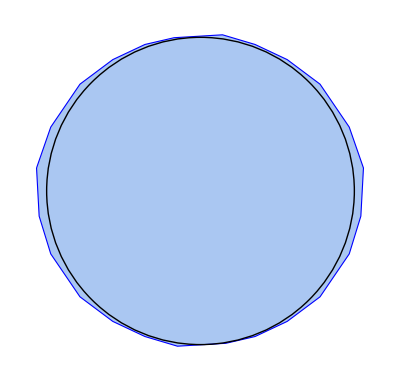

```mathematica
cell=ImageMesh@Import[dir<>"Set 2\\imageset2\\cell.tif"];
rad=41;fitRadius[cell,rad]
```

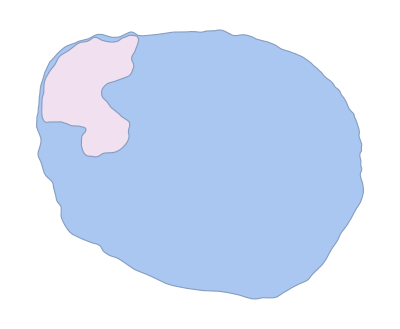

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 2\\imageset2\\imageset2.xlsx","Data"]][[All,3;;4]];
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→87.7764,y→1299.55,u→1367.22,v→368.553}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
mean=Mean@meshCoords;
```

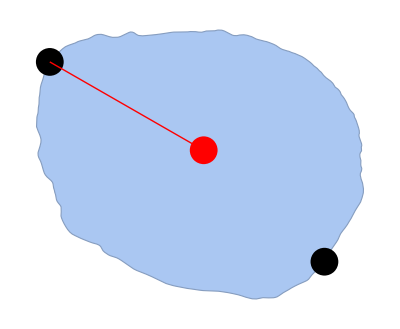

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p1}]}],
ImageSize->Tiny]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1692.62
1. | 0. | 83.1811
0. | 0. | 1.)]

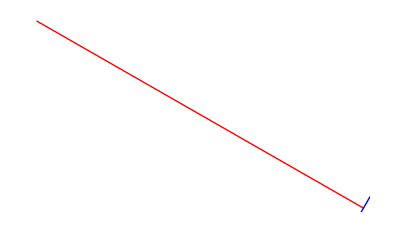

```mathematica
Graphics[{Red,Line[{mean,p1}],Blue,InfiniteLine[{mean,rot@p1}]},ImageSize->Tiny]
```

```mathematica
poly=convertPoly[Subscript[ℛ, 1]]
```

Polygon[…]

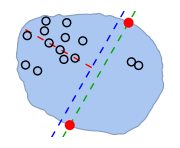

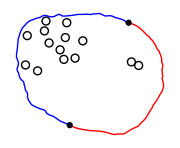

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p1,p2,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

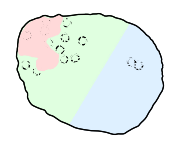

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{699298.,157976.,654142.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{3,0.0000189903}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{9,0.0000128701}

```mathematica
{cRear,dRear}={#1,#1/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{2,3.05744×10^-6}

```mathematica
dMid/dRear
```

4.20942

## set 10

```mathematica
mask=Import[dir<>"Set 2\\imageset3\\Whole Mask.tif"];
ecad=Import[dir<>"Set 2\\imageset3\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

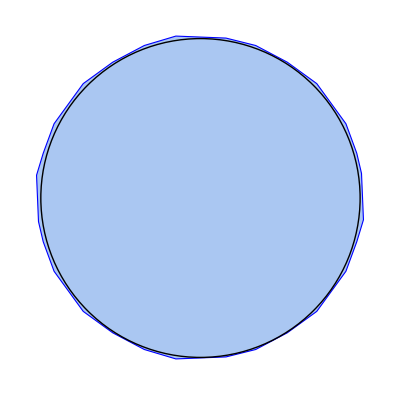

```mathematica
cell=ImageMesh@Import[dir<>"Set 2\\imageset3\\cell.tif"];
rad=43;fitRadius[cell,rad]
```

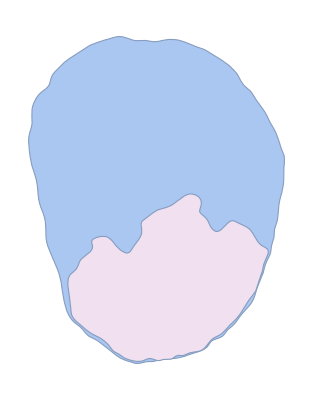

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 2\\imageset3\\imageset4.xlsx","Data"]][[All,3;;4]];
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→700.499,y→11.9667,u→746.5,v→1578.02}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
mean=Mean@meshCoords;
```

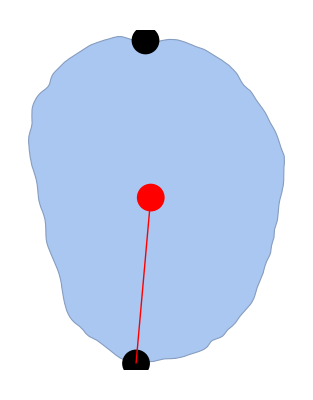

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p1}]}],
ImageSize->Tiny]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1588.22
1. | 0. | 44.2101
0. | 0. | 1.)]

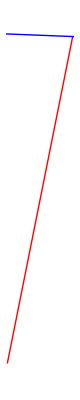

```mathematica
Graphics[{Red,Line[{mean,p1}],Blue,InfiniteLine[{mean,rot@p1}]},ImageSize->Tiny]
```

InfiniteLine[{{-340.037,1255.59},{802.041,1154.04}}]

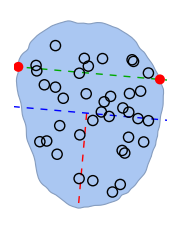

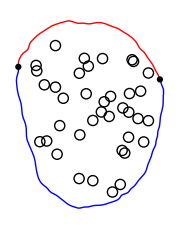

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p1,p2,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

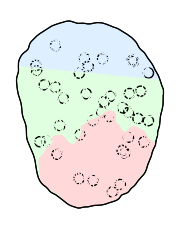

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{622049.,507200.,391370.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1-1,(#1-1)/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{10,0.0000197161}

```mathematica
{cMid,dMid}={#+1,(#1+1)/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{20,0.0000321518}

```mathematica
{cRear,dRear}={#1,(#1)/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{8,0.000020441}

```mathematica
dMid/dRear
```

1.57291

## set 11

```mathematica
mask=Import[dir<>"Set 2\\imageset4\\Whole Mask.tif"];
ecad=Import[dir<>"Set 2\\imageset4\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

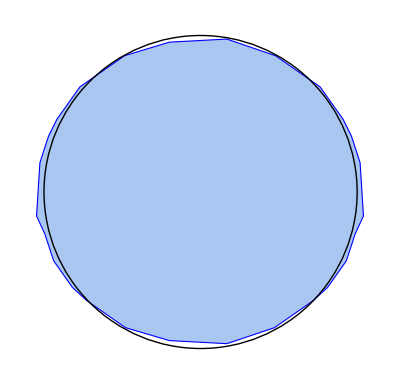

```mathematica
cell=ImageMesh@Import[dir<>"Set 2\\imageset4\\cell.tif"];
rad=35;fitRadius[cell,rad]
```

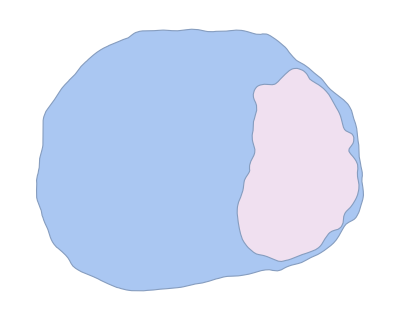

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 2\\imageset4\\imageset5.xlsx","Data"]][[All,3;;4]];
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→1489.01,y→639.5,u→28.9998,v→661.5}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
mean=Mean@meshCoords;
```

```mathematica
{p1,p2}=Graphics`Mesh`FindIntersections[Graphics[{FaceForm[],EdgeForm[Blue],MeshPrimitives[Subscript[ℛ, 1],2],#}]]&[InfiniteLine[{mean,p2}]]
```

{{28.9998,661.5},{1463.16,898.064}}

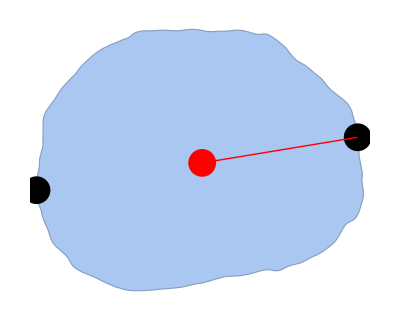

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p2}]}],ImageSize->Tiny]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1552.29
1. | 0. | 14.761
0. | 0. | 1.)]

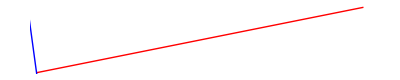

```mathematica
Graphics[{Red,Line[{mean,p2}],Blue,InfiniteLine[{mean,rot@p2}]},ImageSize->Tiny]
```

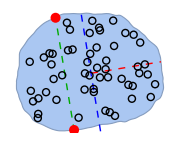

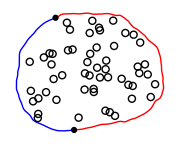

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p2,p1,rad,data]
```

```mathematica
Subscript[ℛ, half2eff]=RegionDifference[Subscript[ℛ, half2],Subscript[ℛ, 2]];
```

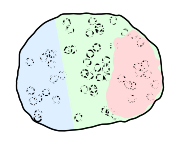

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{606259.,334161.,430794.}}

```mathematica
{{Subscript[Mℛ, half2eff],Subscript[Mℛ, 2],Subscript[Mℛ, half1]},area}=regionMemberFn[Subscript[ℛ, half2eff],Subscript[ℛ, 2],Subscript[ℛ, half1],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{12,0.0000359109}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half2eff]/@dataModified][True],area[[1]]]
```

{28,0.0000461849}

```mathematica
{cRear,dRear}={#1,#1/#2}&[Counts[Subscript[Mℛ, half1]/@dataModified][True],area[[-1]]]
```

{14,0.0000324981}

```mathematica
dMid/dRear
```

1.42115

## set 12

```mathematica
mask=Import[dir<>"Set 2\\imageset5\\Whole Mask.tif"];
ecad=Import[dir<>"Set 2\\imageset5\\Ecad Mask.tif"];
```

```mathematica
HighlightImage[Dilation[MorphologicalPerimeter@mask,5],{Green,ecad},ImageSize->Small]
```

-Graphics-

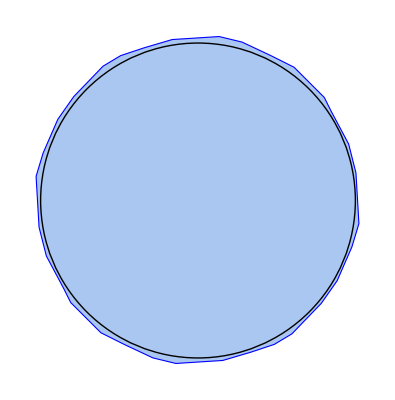

```mathematica
cell=ImageMesh@Import[dir<>"Set 2\\imageset5\\cell.tif"];
rad=40;fitRadius[cell,rad]
```

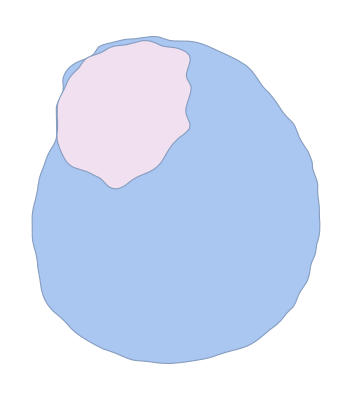

```mathematica
createRegion[mask,ecad]
```

```mathematica
data=First[Import[dir<>"Set 2\\imageset5\\imageset6.xlsx","Data"]][[All,3;;4]];
```

```mathematica
sol=NMaximize[Norm[{x-u,y-v}],{{x,y}∈Subscript[ℛ, 1],{u,v}∈Subscript[ℛ, 1]}]//Quiet//Last
{p1,p2}={{x,y},{u,v}}/.sol;
mean=Mean[{p1,p2}];
centroid=MeshPrimitives[Subscript[ℛ, 1],0]/.Point-> Sequence//Mean;
```

{x→995.242,y→95.5622,u→506.553,v→1477.22}

```mathematica
meshCoords=MeshCoordinates[Subscript[ℛ, 4]];
```

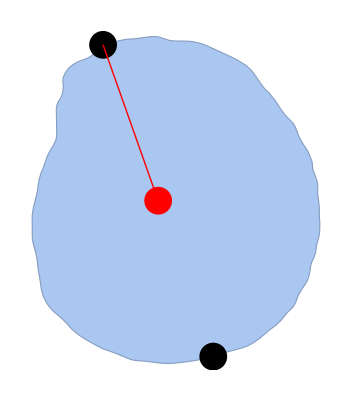

```mathematica
Show[Subscript[ℛ, 1],Graphics[{PointSize[0.05],Point[{p1,p2}],Red,Point@mean,Line[{mean,p2}]}],ImageSize->Tiny]
```

```mathematica
dataModified=Abs[#-{0,1600}]&/@data;
```

```mathematica
rot=RotationTransform[90Degree,mean]
```

TransformationFunction[(0. | -1. | 1537.29
1. | 0. | 35.4958
0. | 0. | 1.)]

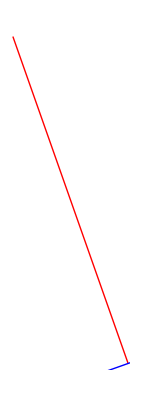

```mathematica
Graphics[{Red,Line[{mean,p2}],Blue,InfiniteLine[{mean,rot@p2}]},ImageSize->Tiny]
```

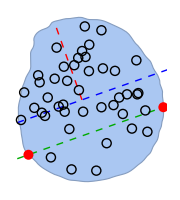

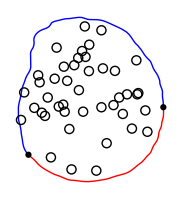

{Polygon[…],Polygon[…]}

```mathematica
{Subscript[ℛ, half2],Subscript[ℛ, half1]}=dividePoly[Subscript[ℛ, 1],Subscript[ℛ, 2],mean,rot,p2,p1,rad,data]
```

```mathematica
Subscript[ℛ, half1eff]=RegionDifference[Subscript[ℛ, half1],Subscript[ℛ, 2]];
```

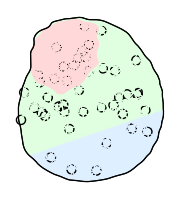

{{RegionMemberFunction[…],RegionMemberFunction[…],RegionMemberFunction[…]},{778487.,293908.,392989.}}

```mathematica
{{Subscript[Mℛ, half1eff],Subscript[Mℛ, 2],Subscript[Mℛ, half2]},area}=regionMemberFn[Subscript[ℛ, half1eff],Subscript[ℛ, 2],Subscript[ℛ, half2],Subscript[ℛ, 4],rad,data]
```

```mathematica
{cTip,dTip}={#1,#1/#2}&[Counts[Subscript[Mℛ, 2]/@dataModified][True],area[[2]]]
```

{13,0.0000442316}

```mathematica
{cMid,dMid}={#,#/#2}&[Counts[Subscript[Mℛ, half1eff]/@dataModified][True],area[[1]]]
```

{24,0.000030829}

```mathematica
{cRear,dRear}={#1,#1/#2}&[Counts[Subscript[Mℛ, half2]/@dataModified][True],area[[-1]]]
```

{6,0.0000152676}

```mathematica
dMid/dRear
```

2.01925

# distribution

```mathematica
p={
{0.0000442315668672472,0.00003082901964938204,0.00001526759417326186},
{0.000035910884329654616,0.00004618485943790366,0.00003249812308347217},
{0.00001971609139627077,0.000032151823395669136,0.000020441033611897675},
{0.000018990276650104524,0.00001287005444954421,3.0574381698703497*^-6},
{0.00002119856171013329,0.000016211024516561163,0.000018676802028312967},
{0.000014791191629985839,0.000023981133750455877,0.000025811038482952645},
{0.000028666266566295787,0.000023713050148149076,0.00001791286409456585},
{0.00003745856709178008,0.000045064744632783366,0.00004320924640145533},
{0.000030483671814254204,0.00003743057999442441,0.000014503625898510913},
{0.000039138607467757964,0.00004664431417608802,0.000039486056282578046},
{0.000020491102287881677,0.000024809619779951894,5.841695342610324*^-6}
};
```

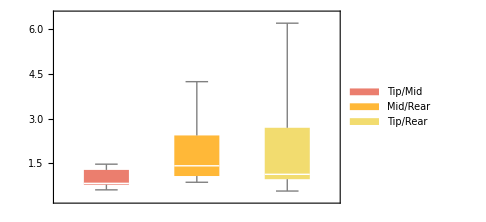
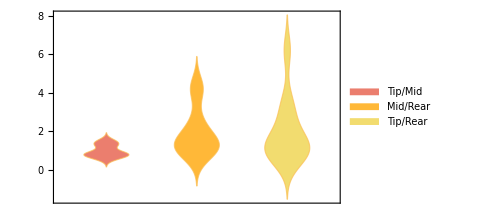

```mathematica
{BoxWhiskerChart[{p[[All,1]]/p[[All,2]],p[[All,2]]/p[[All,-1]],p[[All,1]]/p[[All,-1]]},
ChartLegends-> {"Tip/Mid","Mid/Rear","Tip/Rear"},ChartStyle->24,ImageSize->Medium],DistributionChart[{p[[All,1]]/p[[All,2]],p[[All,2]]/p[[All,-1]],p[[All,1]]/p[[All,-1]]},
ChartLegends-> {"Tip/Mid","Mid/Rear","Tip/Rear"},ChartStyle->24,ImageSize->Medium]}
```

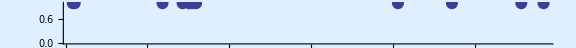

```mathematica
NumberLinePlot[(p[[All,1]]/p[[All,2]]),PlotStyle->{PointSize[0.015],ColorData[1][1]},ImageSize->Large,Background->LightBlue]
```

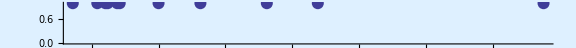

```mathematica
NumberLinePlot[(p[[All,1]]/p[[All,-1]]),PlotStyle->{PointSize[0.015],ColorData[1][1]},ImageSize->Large,Background->LightBlue]
```

```mathematica
ratioMidToRear = {2.02,1.42,1.57,4.21,0.87,0.93,1.32,1.04,2.58,1.18,4.25};
```

```mathematica
Length[ratioMidToRear]
```

11

```mathematica
Through[{Median,Mean}@ratioMidToRear]
```

{1.42,1.94455}

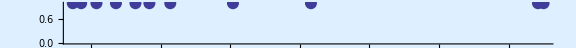

```mathematica
NumberLinePlot[ratioMidToRear,PlotStyle->{PointSize[0.015],ColorData[1][1]},ImageSize->Large,Background->LightBlue]
```

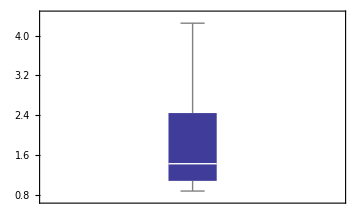
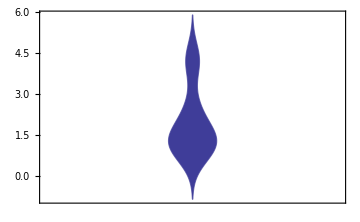

```mathematica
Through[{BoxWhiskerChart[#,ChartStyle->1,ImageSize->Medium]&,
DistributionChart[#,ChartStyle->1,ImageSize->Medium]&}[#]]&[ratioMidToRear]
```